### Parameter and function definitions

#### Clear notebook

```mathematica
ClearAll["Global`*"];
```

#### Rate and diffusion constants

```mathematica
kAct=200; (* μM^-1 s^-1 activation rate of calcium *)
kInact = 1000; (* s^-1 inactivation rate of calcium *)
kTrap = 30; (* μM^-1 s^-1 trapping rate of calcium by DMNP *)
kRel = 7*10^4; (* s^-1 release rate of calcium by DMNP when light is on*)
kIBind = 10; (* μM^-1 s^-1 binding rate of inactivated TCB2 *)
kIUnbind = 1; (* s^-1 unbinding rate of inactivated TCB2 *)
kABind = 10; (* μM^-1 s^-1 binding rate of activated TCB2 *)
kAUnbind = 0; (* s^-1 unbinding rate of activated TCB2 *)

CSat = 6500; (* μM, saturation concentration of bound TCB2 *)

DT = 50; (* μm^2/s, diffusion constant for TCB2 *)
DD = 100; (* μm^2/s, diffusion constant for DMNP *)
DC = 500;(* μm^2/s, diffusion constant for calcium *)
```

#### Initial values

```mathematica
CDI0=0; (* μM *)
CDA0=0; (* μM *)
CBI0=1300; (* μM *)
CBA0=0; (* μM *)
CC0=0; (* μM *)
CDst0=20000; (* μM *)
CD0=20000; (* μM *)
```

#### Domain values

```mathematica
xMax = 100; (* μm *)
yMax = 100; (* μm *)
tMax = 100; (* s *)
```

#### Light activation values

```mathematica
width = 2; (* μm, width of gaussian beam *)
r0 =30; (* μm, radius of circle *)
freq=0.1;(* s^-1, frequency of oscillation *)
duty = 0.25;
```

#### Mechanical values

```mathematica
μ0 = 10^-6*1500; (* Pa, 1st Lame modulus slope *)
λ0 = 10^-6*3000;(* Pa, 2nd Lame modulus slope *)
gMin = 0.5; (* shrinking factor of activated TCB2 *)
γS = 200; (* Pa*s/μm^2, Stokes drag coefficient*)
```

### Function definitions

#### Helper functions

```mathematica
BS[CB_]:=CSat^2/4-(CB-CSat/2)^2; (* concentration of available binding sites *)
gaussian[r_,r0_,s_]:=Exp[-1/2((r-r0)/s)^2];
spaceFunc[r_,r0_,s_]:=1/2*(1-Tanh[(r-r0)/s]);

rFunc[x_,y_,x0_,y0_]:=Sqrt[(x-x0)^2+(y-y0)^2];

WaveFunc[t_,f_,duty_]:=UnitBox[Mod[t*f,1]/(2 duty)];

γFunc[x_,y_,t_]:=spaceFunc[rFunc[x,y,xMax/2,yMax/2],r0,width]*WaveFunc[t,freq,duty];(* external light field *)
pA[CBA_,CBI_]:=CBA/(CBA+CBI);

g[CBA_,CBI_]:=1-(1-gMin)*pA[CBA,CBI];
```

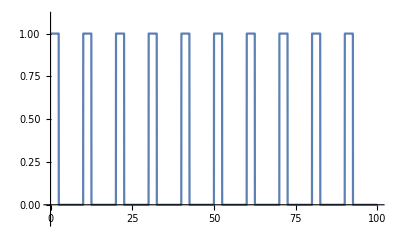

```mathematica
Plot[WaveFunc[t,freq,duty],{t,0,tMax},PlotRange->{-0.1,1.1}]
```

```mathematica
Manipulate[Plot3D[γFunc[x,y,t],{x,0,xMax},{y,0,yMax},PlotRange->{0,1.1},PlotPoints->50],{t,0,tMax}]
```

#### Chemical rate equations

```mathematica
RDI[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kAct*CDI*CC + kInact*CDA-kIBind*CDI*BS[CBA + CBI] + kIUnbind*CBI;
RDA[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=kAct*CDI*CC - kInact*CDA-kABind*CDA*BS[CBA + CBI]+kAUnbind*CBA;

RBI[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kAct*CBI*CC+kInact*CBA+kIBind*CDI*BS[CBA + CBI]-kIUnbind*CBI;
RBA[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=kAct*CBI*CC-kInact*CBA+kABind*CDA*BS[CBA + CBI]-kAUnbind*CBA;

(*RC[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kAct*(CDI+CBI)*CC + kInact*(CDA+CBA)-kTrap*(1-γFunc[x,y,t])*CDst*CC+kRel0*γFunc[x,y,t]*CD;
RD[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=kTrap*(1-γFunc[x,y,t])*CDst*CC-kRel0*γFunc[x,y,t]*CD;
RDst[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kTrap*(1-γFunc[x,y,t])*CDst*CC+kRel0*γFunc[x,y,t]*CD;*)
RC[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kAct*(CDI+CBI)*CC + kInact*(CDA+CBA)-kTrap*CDst*CC+kRel*γFunc[x,y,t]*CD;
RD[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=kTrap*CDst*CC-kRel*γFunc[x,y,t]*CD;
RDst[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kTrap*CDst*CC+kRel*γFunc[x,y,t]*CD;
```

#### Mechanical force function

```mathematica
gradpA[ind_,CBA_,CBI_]:=(gMin-1)/(CBA+CBI)*((1-pA[CBA,CBI])*D[CBA,ind] - pA[CBA,CBI]*D[CBI,ind]);
strainxx[ux_,uy_]:=D[ux,x];
strainxy[ux_,uy_]:=1/2(D[ux,y]+D[uy,x]);
strainyx[ux_,uy_]:=strainxy[ux,uy];
strainyy[ux_,uy_]:=D[uy,y];
divu[ux_,uy_]:=D[ux,x]+D[uy,y];
gradiTr[ind_,ux_,uy_]:=D[divu[ux,uy],ind];

lapui[ui_]:=D[ui,{x,2}]+D[ui,{y,2}]
forcex[x_,y_,ux_,uy_,CBA_,CBI_]:= 2 μ0 *(
 ((D[CBA+CBI,x]*strainxx[ux,uy] +D[CBA+CBI,y]*strainxy[ux,uy])
-1/2 g[CBA,CBI]*D[CBA+CBI,x])+(CBA+CBI)*(1/2(gradiTr[x,ux,uy] + lapui[ux]) - 1/2 gradpA[x,CBA,CBI]))+λ0*(D[CBA+CBI,x]*(divu[ux,uy] - g[CBA,CBI])+(CBA+CBI)*(gradiTr[x,ux,uy]-gradpA[x,CBA,CBI]));

forcey[x_,y_,ux_,uy_,CBA_,CBI_]:= 2 μ0 *(
 ((D[CBA+CBI,x]*strainyx[ux,uy] +D[CBA+CBI,y]*strainyy[ux,uy])
-1/2 g[CBA,CBI]*D[CBA+CBI,y])+(CBA+CBI)*(1/2(gradiTr[y,ux,uy] + lapui[uy]) - 1/2 gradpA[y,CBA,CBI]))+λ0*(D[CBA+CBI,y]*(divu[ux,uy] - g[CBA,CBI])+(CBA+CBI)*(gradiTr[y,ux,uy]-gradpA[y,CBA,CBI]));
```

### Set up differential equation

#### Define differential equations

```mathematica
pdes={
D[CDI[x,y,t],t]==RDI[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DT*Laplacian[CDI[x,y,t],{x,y}],
D[CDA[x,y,t],t]==RDA[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DT*Laplacian[CDA[x,y,t],{x,y}],

D[CBI[x,y,t],t]==RBI[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]- 1/γS(D[forcex[x,y,ux[x,y,t],uy[x,y,t],CBA[x,y,t],CBI[x,y,t]]*CBI[x,y,t],x]+D[forcey[x,y,ux[x,y,t],uy[x,y,t],CBA[x,y,t],CBI[x,y,t]]*CBI[x,y,t],y]),
D[CBA[x,y,t],t]==RBA[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]- 1/γS(D[forcex[x,y,ux[x,y,t],uy[x,y,t],CBA[x,y,t],CBI[x,y,t]]*CBA[x,y,t],x]+D[forcey[x,y,ux[x,y,t],uy[x,y,t],CBA[x,y,t],CBI[x,y,t]]*CBA[x,y,t],y]),

D[CC[x,y,t],t]==RC[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DC*Laplacian[CC[x,y,t],{x,y}],
D[CD[x,y,t],t]==RD[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DD*Laplacian[CD[x,y,t],{x,y}],
D[CDst[x,y,t],t]==RDst[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DD*Laplacian[CDst[x,y,t],{x,y}],

D[ux[x,y,t],t]==1/γS*forcex[x,y,ux[x,y,t],uy[x,y,t],CBA[x,y,t],CBI[x,y,t]],
D[uy[x,y,t],t]==1/γS*forcey[x,y,ux[x,y,t],uy[x,y,t],CBA[x,y,t],CBI[x,y,t]]


};
```

#### Define initial conditions

```mathematica
ics={
CDI[x,y,0]==CDI0,
CDA[x,y,0]==CDA0,

CBI[x,y,0]==CBI0,
CBA[x,y,0]==CBA0,

CC[x,y,0]==CC0,
CD[x,y,0]==CD0,
CDst[x,y,0]==CDst0,

ux[x,y,0]==0,
uy[x,y,0]==0
};
```

#### Define boundary conditions

```mathematica
bcs={
Derivative[1,0,0][CDI][0,y,t]==0,
Derivative[1,0,0][CDI][xMax,y,t]==0,
Derivative[0,1,0][CDI][x,0,t]==0,
Derivative[0,1,0][CDI][x,yMax,t]==0,

Derivative[1,0,0][CDA][0,y,t]==0,
Derivative[1,0,0][CDA][xMax,y,t]==0,
Derivative[0,1,0][CDA][x,0,t]==0,
Derivative[0,1,0][CDA][x,yMax,t]==0,

Derivative[1,0,0][CBA][0,y,t]==0,
Derivative[1,0,0][CBA][xMax,y,t]==0,
Derivative[0,1,0][CBA][x,0,t]==0,
Derivative[0,1,0][CBA][x,yMax,t]==0,

Derivative[1,0,0][CBI][0,y,t]==0,
Derivative[1,0,0][CBI][xMax,y,t]==0,
Derivative[0,1,0][CBI][x,0,t]==0,
Derivative[0,1,0][CBI][x,yMax,t]==0,

Derivative[1,0,0][CC][0,y,t]==0,
Derivative[1,0,0][CC][xMax,y,t]==0,
Derivative[0,1,0][CC][x,0,t]==0,
Derivative[0,1,0][CC][x,yMax,t]==0,

Derivative[1,0,0][CD][0,y,t]==0,
Derivative[1,0,0][CD][xMax,y,t]==0,
Derivative[0,1,0][CD][x,0,t]==0,
Derivative[0,1,0][CD][x,yMax,t]==0,

Derivative[1,0,0][CDst][0,y,t]==0,
Derivative[1,0,0][CDst][xMax,y,t]==0,
Derivative[0,1,0][CDst][x,0,t]==0,
Derivative[0,1,0][CDst][x,yMax,t]==0,



ux[0,y,t]==0,
ux[xMax,y,t]==0,
ux[x,0,t]==0,
ux[x,yMax,t]==0,

Derivative[1,0,0][ux][0,y,t]==0,
Derivative[1,0,0][ux][xMax,y,t]==0,
Derivative[0,1,0][ux][x,0,t]==0,
Derivative[0,1,0][ux][x,yMax,t]==0,

uy[0,y,t]==0,
uy[xMax,y,t]==0,
uy[x,0,t]==0,
uy[x,yMax,t]==0,

Derivative[1,0,0][uy][0,y,t]==0,
Derivative[1,0,0][uy][xMax,y,t]==0,
Derivative[0,1,0][uy][x,0,t]==0,
Derivative[0,1,0][uy][x,yMax,t]==0
};
```

### Solve the differential equation

```mathematica
sol=NDSolve[{pdes,bcs,ics},
{CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t],ux[x,y,t],uy[x,y,t]},
{x,0,xMax},
{y,0,yMax},
{t,0,tMax/200},AccuracyGoal->2];
(*Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->15,"MaxPoints"->300}},
AccuracyGoal->10];
*)
CDISol[x_,y_,t_]:=Evaluate[CDI[x,y,t]/.sol];
CDASol[x_,y_,t_]:=Evaluate[CDA[x,y,t]/.sol];
CBISol[x_,y_,t_]:=Evaluate[CBI[x,y,t]/.sol];
CBASol[x_,y_,t_]:=Evaluate[CBA[x,y,t]/.sol];
CCSol[x_,y_,t_]:=Evaluate[CC[x,y,t]/.sol];
CDSol[x_,y_,t_]:=Evaluate[CD[x,y,t]/.sol];
CDstSol[x_,y_,t_]:=Evaluate[CDst[x,y,t]/.sol];
uxSol[x_,y_,t_]:=Evaluate[ux[x,y,t]/.sol];
uySol[x_,y_,t_]:=Evaluate[uy[x,y,t]/.sol];
```

$Aborted

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Manipulate[Plot3D[CCSol[x,y,t],{x,0,xMax},{y,0,yMax},PlotRange->{0,CC0}],{t,0,tMax}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00715,0.00715,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{CDI^(0,0,1)[0.00715,0.00715,3.]==RDI[0.00715,0.00715,3.,CDI[«3»],CDA[«3»],CBI[«3»],CBA[«3»],CC[«3»],CD[«3»],CDst[«3»]]+Plus[«2»]/200000000,«5»,CDst^(0,0,1)[0.00715,0.00715,3.]==RDst[0.00715,0.00715,3.,CDI[«3»],CDA[«3»],CBI[«3»],CBA[«3»],CC[«3»],CD[«3»],CDst[«3»]]+Plus[«2»]/100000000},{«1»},{CDI[0.00715,0.00715,0]==0,«5»,«1»==20000}},«6»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 7.15001 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00715,0.00715,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{pdes,{},ics},{CDI[0.00715,0.00715,3.],CDA[0.00715,0.00715,3.],CBI[0.00715,0.00715,3.],CBA[0.00715,0.00715,3.],CC[0.00715,0.00715,3.],CD[0.00715,0.00715,3.],CDst[0.00715,0.00715,3.]},«4»,AccuracyGoal→10]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{pdes,{},ics},{CDI[0.00715,0.00715,3.],CDA[0.00715,0.00715,3.],CBI[0.00715,0.00715,3.],CBA[0.00715,0.00715,3.],CC[0.00715,0.00715,3.],CD[0.00715,0.00715,3.],CDst[0.00715,0.00715,3.]},«4»,AccuracyGoal→10.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 7.15001 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{pdes,{},ics},{CDI[7.15001,0.00715,3.],CDA[7.15001,0.00715,3.],CBI[7.15001,0.00715,3.],CBA[7.15001,0.00715,3.],CC[7.15001,0.00715,3.],CD[7.15001,0.00715,3.],CDst[7.15001,0.00715,3.]},«4»,AccuracyGoal→10]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00715,0.00715,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00715,0.00715,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00715,0.00715,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00715,0.00715,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»,{CDI[0.00715,0.00715,3.],CDA[0.00715,0.00715,3.],CBI[0.00715,0.00715,3.],CBA[0.00715,0.00715,3.],CC[0.00715,0.00715,3.],CD[0.00715,0.00715,3.],CDst[0.00715,0.00715,3.]},«3»,Method→{MethodOfLines,«1»,SpatialDiscretization→{FiniteElement,«1»,Ma…ts→300}},AccuracyGoal→2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 7.15001 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»,{CDI[0.00715,0.00715,3.],CDA[0.00715,0.00715,3.],CBI[0.00715,0.00715,3.],CBA[0.00715,0.00715,3.],CC[0.00715,0.00715,3.],CD[0.00715,0.00715,3.],CDst[0.00715,0.00715,3.]},«3»,Method→{MethodOfLines,Tempo…iable→3.,SpatialDiscretization→{FiniteElement}},AccuracyGoal→2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 7.15001 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»,{CDI[0.00715,0.00715,3.],CDA[0.00715,0.00715,3.],CBI[0.00715,0.00715,3.],CBA[0.00715,0.00715,3.],CC[0.00715,0.00715,3.],CD[0.00715,0.00715,3.],CDst[0.00715,0.00715,3.]},«3»,Method→{MethodOfLines,Tempo…iable→3.,SpatialDiscretization→{FiniteElement}},AccuracyGoal→2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 7.15001 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.00715,0.00715,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot3D::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

General::prng: Value of option PlotRange -> {0,CC0} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Manipulate[Plot3D[CBASol[x,y,t]+CBISol[x,y,t],{x,0,xMax},{y,0,yMax},PlotRange->{0,8}],{t,0,tMax}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[Plot[CBASol[x,5,t]+CBISol[x,5,t],{x,0,xMax},PlotRange->{0,CSat+1}],{t,0,tMax}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {0,1+CSat} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Manipulate[
VectorPlot[{uxSol[x,y,t][[1]],uySol[x,y,t][[1]]},{x,0,xMax},{y,0,yMax}]
,{t,0,tMax}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

VectorPlot::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

```mathematica
pos[Ri_,t_]:=Ri + 5*{uxSol[Ri[[1]],Ri[[2]],t][[1]],uySol[Ri[[1]],Ri[[2]],t][[1]]}
fac = 20;
Ris = Flatten[Table[{i,j},{i,0,xMax,xMax/fac},{j,0,yMax,yMax/fac}],1];
funcArray[t_]:=Table[pos[Ris[[i]],t],{i,1,Length[Ris]}]
Manipulate[ListPlot[funcArray[t],AspectRatio->1,PlotRange->{{-1,xMax+1},{-1,yMax+1}}],{t,0,tMax}]
```

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

General::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

General::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[Plot[pA[CBASol[x,y,t],CBISol[x,y,t]],{t,0,tMax},PlotRange->{0,1}],{x,0,xMax},{y,0,yMax}]
```

NDSolve::dsvar: 9.5 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 9.5 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 9.5 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»,{CDI[9.5,10.35,0.00204286],CDA[9.5,10.35,0.00204286],CBI[9.5,10.35,0.00204286],CBA[9.5,10.35,0.00204286],CC[9.5,10.35,0.00204286],CD[9.5,10.35,0.00204286],CDst[9.5,10.35,0.00204286],ux[9.5,10.35,0.00204286],uy[9.5,10.35,0.00204286]},«3»,Method→{«1»},AccuracyGoal→10.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::plln: Limiting value tMax in {t,0,tMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{uxSol[x,y,t],uySol[x,y,t]},{t,0,tMax},PlotRange->{-0.05,0.05}],{x,0,xMax},{y,0,yMax}]
```

NDSolve::dsvar: 10.34 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{CDI^(0,0,1)[10.34,11.34,0.00204286]==CBI[10.34,11.34,0.00204286]+1000 CDA[«3»]-10 Plus[«2»] CDI[«3»]-200 CC[«3»] CDI[«3»]+50 Plus[«2»],CDA^(0,0,1)[10.34,11.34,0.00204286]==-1000 CDA[«3»]-10 Plus[«2»] CDA[«3»]+200 CC[«3»] CDI[«3»]+50 Plus[«2»],«5»,ux^(0,0,1)[10.34,11.34,0.00204286]==0,uy^(0,0,1)[10.34,11.34,0.00204286]==0},{«1»},{CDI[10.34,11.34,0]==0,CDA[10.34,11.34,0]==0,«5»,ux[10.34,11.34,0]==0,uy[10.34,11.34,0]==0}},«5»,AccuracyGoal→10]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 10.34 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{CDI^(0,0,1)[10.34,11.34,0.00204286]==CBI[10.34,11.34,0.00204286]+1000. CDA[«3»]-10. Plus[«2»] CDI[«3»]-200. CC[«3»] CDI[«3»]+50. Plus[«2»],CDA^(0,0,1)[10.34,11.34,0.00204286]==-1000. CDA[«3»]-10. Plus[«2»] CDA[«3»]+200. CC[«3»] CDI[«3»]+50. Plus[«2»],«5»,ux^(0,0,1)[10.34,11.34,0.00204286]==0.,uy^(0,0,1)[10.34,11.34,0.00204286]==0.},{«1»},{CDI[10.34,11.34,0.]==0.,«7»,uy[10.34,11.34,0.]==0.}},«5»,AccuracyGoal→10.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 10.34 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::plln: Limiting value tMax in {t,0,tMax} is not a machine-sized real number.